# Thesis Notebook

## 2D Orbit with the suns density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

### Matex

```mathematica
(*1. GLOBAL CONFIGURATION*)Needs["MaTeX`"];
exportDirectory="/home/em/Documents/thesis/sun_density";
If[!FileExistsQ[exportDirectory],CreateDirectory[exportDirectory]];

(*Global Styling Variables*)
$ThesisFontSize=20;
$ThesisTickSize=14;
$ThesisImageSize=450; (*Slightly larger as requested*)
$ThesisThickness=2.0;
$GridStyle=Directive[GrayLevel[0.9],AbsoluteThickness[0.5]];
$FrameStyle=Directive[Black,AbsoluteThickness[1.2]];

(*REVERTED TO ORIGINAL COLORS*)
$ThesisColors={Blue,Red,Green,Purple,Darker[Green]};

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath, amsfonts, amssymb, amsthm, bm, lmodern}","\\newcommand{\\rb}{\\bar{r}}","\\providecommand{\\e}[1]{\\ensuremath{\\times 10^{#1}}}"}];

ThesisStandardPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\rb)",xLabel_:"\\rb",labels_List:{},xTick_:None,pPoints_:100,wPrec_:30,customStyles_:{}]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,usedStyles},ticks={Automatic,Automatic};
grid=Automatic;
(*Logic for specific xTick (r0)*)If[xTick=!=None,ticks={{Automatic,Automatic},{Union[FindDivisions[{vMin,vMax},6],{{xTick,MaTeX["\\bar{r}_0",FontSize->$ThesisFontSize]}}],Automatic}};
grid={{xTick},Automatic};];
(*Determine Styles:Use custom list if provided,else use default ThesisColors*)usedStyles=If[customStyles==={},Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],customStyles];
plotOptions={Frame->True,Axes->False,PlotStyle->usedStyles,FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->Scaled[0.04],PlotPoints->pPoints,MaxRecursion->6,WorkingPrecision->wPrec,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Standard (High-Precision): ",Green,Bold],fullPath];
finalPlot]

ThesisStandardPlotPOL[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\rb)",xLabel_:"\\rb",labels_List:{},xTick_:None,pPoints_:100,wPrec_:30,customStyles_:{}]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,usedStyles},ticks={Automatic,Automatic};
grid=Automatic;
(*Logic for specific xTick (r0)*)If[xTick=!=None,ticks={{Automatic,Automatic},{Union[FindDivisions[{vMin,vMax},6],{{xTick,MaTeX["\\bar{r}_0",FontSize->$ThesisFontSize]}}],Automatic}};
grid={{xTick},Automatic};];
(*Determine Styles:Use custom list if provided,else use default ThesisColors*)usedStyles=If[customStyles==={},Table[{If[i==2,Directive[$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],Opacity[0.75]],$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],customStyles];
plotOptions={Frame->True,Axes->False,PlotStyle->usedStyles,FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->Scaled[0.04],PlotPoints->pPoints,MaxRecursion->6,WorkingPrecision->wPrec,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Standard (High-Precision): ",Green,Bold],fullPath];
finalPlot]

(*2b.TIME PLOT FUNCTION-Font Matched to Standard Plot*)(*2b.TIME PLOT FUNCTION-Forced Ticks and Matched Fonts*)(*2b.TIME PLOT FUNCTION-Forced Ticks,Matched Fonts,2-Digit Precision*)ThesisStandardPlotTime[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f",xLabel_:"t",labels_List:{},xTick_:None,pPoints_:100,wPrec_:30]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,xDivs,proximityThreshold,xTickLabels},(*1. Force exactly 4 ticks*)xDivs=N[Subdivide[vMin,vMax,3]];
grid={xDivs,Automatic};
(*2. Create the labels with exactly 2 digits of precision*)(*NumberForm[val,2] ensures "1.0" or "1.1" style formatting*)xTickLabels=Table[{val,NumberForm[val,2]},{val,xDivs}];
If[xTick=!=None,proximityThreshold=(vMax-vMin)*0.15;
ticks={{Automatic,Automatic},{Union[(*Filter out the auto-generated ticks too close to your t_s*)Select[xTickLabels,Abs[#[[1]]-xTick]>proximityThreshold&],{{xTick,MaTeX["t_{\\text{s}}",FontSize->$ThesisFontSize]}}],None}};
grid={{xTick},Automatic};,(*If no xTick,use the rounded subdivisions*)ticks={Automatic,{xTickLabels,None}};];
plotOptions={Frame->True,Axes->False,PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->{Scaled[0.05],Scaled[0.1]},PlotPoints->pPoints,WorkingPrecision->wPrec,MaxRecursion->6,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Fixed Plot (2-Digit Precision): ",Black,Bold],fullPath];
finalPlot]

(*2c.PIECEWISE PLOT FUNCTION-Updated for Round Numbers*)
ThesisPiecewisePlot[func_,{var_,vMin_,vMax_},rStar_,fileName_String,yLabel_:"f(\\bar{r})",xLabel_:"\\bar{r}",labels_List:{},xTick_:None]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,xDivs,proximityThreshold},ticks={Automatic,Automatic};grid={Automatic,Automatic};
If[xTick=!=None,xDivs=FindDivisions[{vMin,vMax},6];
proximityThreshold=(vMax-vMin)*0.08;
ticks={{Automatic,Automatic},{Union[Select[xDivs,Abs[#-xTick]>proximityThreshold&],{{xTick,MaTeX["\\rb_0",FontSize->$ThesisFontSize]}}],None}};];
plotOptions={Frame->True,Axes->False,ColorFunction->Function[{x,y},If[x<rStar,Blue,Red]],ColorFunctionScaling->False,PlotStyle->{AbsoluteThickness[$ThesisThickness+0.5]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->{Scaled[0.02],Scaled[0.1]},Exclusions->None,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[func,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[{Blue,Red},MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize,FontFamily->"Latin Modern Roman"}],{0.2,0.75}]],Plot[func,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Piecewise: ",Green,Bold],fullPath];finalPlot]

(*3. MASTER ORBIT FUNCTION (2D Spatial)*)ThesisOrbitPlot[{xFunc_,yFunc_},{var_,vMin_,vMax_},rStar_,fileName_String,xLabel_:"\\bar{r}(t)\\cos(\\phi(t))",yLabel_:"\\bar{r}(t)\\sin(\\phi(t))",xTick_:None]:=Module[{orbitLine,body,finalPlot,fullPath,ticks,extras,startPos,plotBoundaries,xDivs,xRangeWidth},orbitLine=ParametricPlot[{xFunc,yFunc},{var,vMin,vMax},PlotStyle->{Black,AbsoluteThickness[1.5]},PlotPoints->300];
body=Graphics[{Yellow,EdgeForm[{Yellow,AbsoluteThickness[1]}],Disk[{0,0},rStar]}];
ticks={Automatic,Automatic};extras={};
If[xTick=!=None,startPos={xFunc,yFunc}/. var->vMin;
extras={Directive[GrayLevel[0.4],Dashed,AbsoluteThickness[1]],InfiniteLine[{xTick,0},{0,1}],Directive[Black],Disk[startPos,Offset[3]]};
plotBoundaries=PlotRange/. AbsoluteOptions[orbitLine,PlotRange];
xRangeWidth=Abs[plotBoundaries[[1,2]]-plotBoundaries[[1,1]]];
xDivs=FindDivisions[plotBoundaries[[1]],6];
xDivs=Select[xDivs,Abs[#-xTick]>0.10*xRangeWidth&];
ticks={{Automatic,Automatic},{Union[Table[{i,i},{i,xDivs}],{{xTick,MaTeX["\\rb_0",FontSize->$ThesisFontSize]}}],Automatic}};];
finalPlot=Show[body,Graphics[extras],orbitLine,Frame->True,Axes->False,AspectRatio->Automatic,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->Automatic,GridLinesStyle->$GridStyle,ImageSize->$ThesisImageSize,PlotRange->All,PlotRangePadding->Scaled[0.08]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Orbit: ",Blue,Bold],fullPath];finalPlot]

(*4. LOGARITHMIC PLOTTING FUNCTION*)
ThesisLogPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f",xLabel_:"t",tSurface_:None]:=Module[{finalPlot,fullPath,ticks,grid},grid={If[NumberQ[tSurface],{tSurface},{}],Automatic};
ticks={Automatic,{Join[FindDivisions[{vMin,vMax},6],If[NumberQ[tSurface],{{tSurface,MaTeX["t_{\\text{s}}",FontSize->$ThesisFontSize]}},{}]],Automatic}};
finalPlot=LogPlot[funcs,{var,vMin,vMax},Frame->True,Axes->False,PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->{{vMin,vMax},All},PlotRangePadding->{None,Scaled[0.05]},Method->{"DefaultBoundaryStyle"->None}];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Log Plot: ",Magenta,Bold],fullPath];finalPlot]

ThesisStandardLogLogPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"m(t)",xLabel_:"t"]:=Module[{finalPlot,fullPath,startPoint},(*LogLogPlot cannot start at 0. We shift to a tiny value if needed*)startPoint=If[vMin==0,10^-3,vMin];
finalPlot=LogLogPlot[funcs,{var,startPoint,vMax},(*Visuals:Matching your Standard Plot exactly*)Frame->True,Axes->False,FrameStyle->$FrameStyle,FrameTicksStyle->Directive[Black,$ThesisTickSize],(*Use Automatic to let Mathematica handle log-spacing correctly*)FrameTicks->{{Automatic,None},{Automatic,None}},GridLines->{Automatic,Automatic},GridLinesStyle->$GridStyle,(*Labels& Sizing*)FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,(*Line Style*)PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],(*Performance*)PlotRange->Automatic];
(*Export logic*)fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Matched Log-Log: ",Black,Bold],fullPath];
finalPlot]
```

### constants

```mathematica
infprec[lowlyprecision_, p_] := 10^-p Round[(10^p) lowlyprecision]
```

```mathematica
(*R values in Schwarzschild coordinates*)
M = 1;
RStarrr = (6.957 10^8)/1480;(*Radius of the Star*)
RStar = infprec[RStarrr, 10];
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r)

```mathematica
rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

```mathematica
rbarStarr = rbarofrOutside[RStar];
rbarStar = infprec[rbarStarr, 40];
```

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2;
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

## Mass and Density functions from 2405.08113

### Fixing the rho0 by letting the total mass integral equal to 1

```mathematica
rho[r_] := rho0(1 - r/R)^6;
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, R}];
```

```mathematica
rhoCentre[R_] := (63M)/(Pi R^3) (*From the above*)
rho0 = rhoCentre[RStar];
```

### Mass function

```mathematica
MassFunc[r_] := 252M(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3))
```

### Density function

```mathematica
rho[r_] :=rho0(1 - r/RStar)^6
```

## Numerically integrating for the pressure and the phi in α = exp(phi)

### Defining the ODEs

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -(rho[r] + Pressure)((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])));
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := ((MassFunc[r] + 4 Pi Pressure r^3)/(r(r-2MassFunc[r])));
```

#### Numerically integrating these coupled ODEs

```mathematica
rmin = 10^-16 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, rmin},
WorkingPrecision->40
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
Pressure[r_] := P[r] /. sol1

PhiMetric[r_] = Phi[r] /. sol1;
```

## Solving for r̄(r) and r(r̄) inside

### Defining the ODE

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

### Numerically Integrating the above equation

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin},
WorkingPrecision->50
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

### Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Table[ expression, {variable, start, end, step}*)
data = Table[
{rbarofrInside[r], r}, 
{r, rmin, RStar, (RStar - rmin)/10000} (*10000 points and A is not messy*)
];
```

```mathematica
rofrbarInside = Interpolation[data];
```

## Finding the interior metric functions

### Getting αInside(r̄):

```mathematica
αInside[rbar_?NumericQ] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

#### Sanity checks

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
(*αFull[rbar_]:=If[rbar<rbarStar,αInside[rbar],α[rbar]]*)
```

### Making the derivative of alpha continuous

#### Interior derivative in terms of r

Doing things in r first as this is more analytic

```mathematica
dPhidrMetric[r_] := ((MassFunc[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFunc[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r] (*Analytic times numerical integral*)
```

Exterior derivative

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2M)/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r] (*Chain rule*)
```

### Checking to see if it worked

### Proper definitions in isotropic coords now

```mathematica
DERαOutside[rbar_] := Module[{r = rofrbarOutside[rbar]}, drbardr[r]  DERαOutsiderbar[r]]

DERαInside[rbar_] := Module[{r = rofrbarInside[rbar]},
dPhidrMetric[r] alpha[r]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

```mathematica
AInside[rbar_] := rofrbarInside[rbar]/rbar;
```

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
(*AFull[rbar_]:=If[rbar<rbarStar,AInside[rbar],A[rbar]]*)
```

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFunc[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
(*DERAFull[rbar_]:=If[rbar<rbarStar,DERAInside[rbar],DERAOutside[rbar]]*)
```

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar];
```

```mathematica
rho[rbar_] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar < rbarStar},
{0, rbar >= rbarStar}
}
];
```

```mathematica
(*Maybe issue with NDSolve is that there are two numerically integrated things here being used and its causing issues?*)
(*Going to make the above as one interpolating function*)
data = Table[{rbarofrInside[r], Pressure[r]},
{r, rmin, RStar, RStar/10000}];
```

```mathematica
IsotropicCoordsPressureee = Interpolation[data];
```

```mathematica
(*Solved the issue of the solver not being able to get an equation for rbar'[t] (method residual error)*)
```

```mathematica
IsotropicCoordsPressure[rbar_] := Pressure[rofrbarInside[rbar]];
```

### Sorting out the speed of sound as a function of r: a(r)

```mathematica
(*Getting the derivative of the density*)
rhodummy[r_] := rho0(1 - r/RStar)^6
rhodummy'[r];
drhodr[r_] := (-6 rho0)/RStar(1-r/RStar)^5
```

#### Speed of sound in isotropic coordinates

```mathematica
rbarStar //N
```

470067.

```mathematica
.999995rbarStar
```

470064.

```mathematica
.999999rbarStar
```

470066.

```mathematica
cutoffIso = .999995rbarStar
```

470064.

```mathematica
asosEndInterp[.9999999rbarStar]
```

asosEndInterp[470067.]

```mathematica
asosEndInterp[rbar_] := Module[{r=rofrbarInside[rbar]},Sqrt[dPdr[r,Pressure[r]]/drhodr[r]]
]
```

```mathematica
data = Prepend[Table[
{rbar, asosEndInterp[rbar]}, 
{rbar, cutoffIso, .999999rbarStar, (rbarStar - cutoffIso)/10000} (*1000 points and A is not messy*)
], {rbarStar, asosEndInterp[.999999rbarStar]}];
```

```mathematica
asosEnd = Interpolation[data]
```

InterpolatingFunction[…]

```mathematica
asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]},Piecewise[{
{Sqrt[dPdr[r,Pressure[r]]/drhodr[r]],rbar<cutoffIso},{asosEnd[rbar],cutoffIso<=rbar<=rbarStar},
{asosEnd[rbarStar], rbar > rbarStar}
}
]
]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/sun_density/Fig_asos.pdf

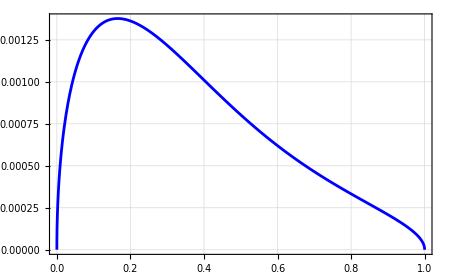

```mathematica
ThesisStandardPlot[asosPiecewise[x*rbarStar],(*1. The function (scaled back to rbar)*){x,0,1},(*2. Plotting from 0 to 1 on the x-axis*)"Fig_asos",(*3. Filename*)"a(\\bar{r})",(*4. y-label*)"\\bar{r}/\\bar{R}^*",(*5. x-label (The scaled label)*){},(*6. No legends*)None,(*7. No specific x-tick*)200,(*8. PlotPoints (Higher for Piecewise)*)30                                (*9. WorkingPrecision*)]
```

## Setting up 2D ODEs for new density profile:

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.9999;
x2=1.0001;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.9999},
{anaylticline[Μach], 0.9999 < Μach  < 1.0001},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.0001}
}];
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
umagOutside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ]:=(√(ur^2+(uphi/rbar)^2))/A[rbar]
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_?NumericQ, rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_?NumericQ, rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] :=((√(ur^2+(uphi/rbar)^2))/AInside[rbar])/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative Forces

Accretion

```mathematica
mdot[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (4Pi rho[rbar] m^2)/((asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
dpdtaccretionr[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -((4 Pi αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))ur;

dpdtaccretionphi[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -((4 Pi αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))uphi
```

Drag

```mathematica
dpdtdragphi[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(rho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (-4π αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
(*Redefining the mass function without the piecewise component for simplicity*)
MassFunction[r_] := 252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3));
```

```mathematica
Mp[r_] := Derivative[1][MassFunction][r]
Mpp[r_] := Derivative[2][MassFunction][r]
Mppp[r_] := Derivative[3][MassFunction][r]
```

```mathematica
FRRrIns[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFunction[r]^2+r MassFunction[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_?NumericQ, rbar_?NumericQ,ur_?NumericQ, uphi_?NumericQ]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFunction[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFunction[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 4/10;
(*eccentricity = 9/11; (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)*)
semilatrecPp = 4 10^5;
semilatrecP = infprec[semilatrecPp, 40];
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity]
```

2000000/(√9999921)

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M]
rbar0 = rbarofrOutside[r0]

rperiapsis[eccentricity, ptilde];
```

2000000/3

1/2 (1999997/3+(2000 √999997)/3)

#### Must satisfy this inequality to pass through star

```mathematica
RStar(1+eccentricity)
```

8226182432432433/12500000000

```mathematica
6 + 2eccentricity
```

34/5

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
t0=0;
tEnd=10^12;
m=5 10^-3;
η =  Max[1,10^-4/m];(*10^16 and 3.8 10^10*) (*su = .94 10^16*)
(*5 10^4 nice su factor*)

NearSubsonicTime = {};

Monitor[
solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"],
WhenEvent[rbar[t] < rbarStar && Mach[rbar[t], ur[t], uphi[t]] <= 2, AppendTo[NearSubsonicTime, {t, rbar[t]}]],
WhenEvent[mass[t]>=0.01, "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->30,

StepMonitor:>(currentTime = t)(*Machine precision and 20k max steps also works*)
][[1]],
Column[{
Row[{"Progress: ", ProgressIndicator[currentTime, {t0, tEnd}]}],
Row[{"Current Time: ", NumberForm[currentTime, {6, 2}], " / ",  tEnd}] (*Amount of digits displayed, amount of decimals rounded*)
}]
];
```

InterpolatingFunction::dmval: Input value {470630.604513173718026633636306} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {470631.60451370492020006168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1.53256901996846912723222724165×10^10 and t = 1.53276394050376948874702137825×10^10.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;

tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,1000000,10,tFinish}];
```

1.60199388950094801921845966296×10^10

```mathematica
(*Bundle your solutions and constants into a list*)dataToSave={rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface};

(*Export using DumpSave-Note:DumpSave requires a Symbol or a list of Symbols*)
DumpSave[FileNameJoin[{exportDirectory,"SunStarSim_Final.mx"}],{rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface}];

Print[Style["Binary .mx file saved. Load speed: Instant.",Green,Bold]];
```

Binary .mx file saved. Load speed: Instant.

```mathematica
Get[FileNameJoin[{exportDirectory,"SunStarSim_Final.mx"}]];
```

Saved Orbit: /home/em/Documents/thesis/sun_density/Fig_Orbit_With_r0.pdf

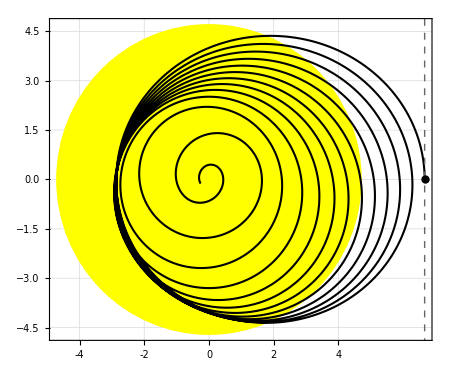

```mathematica
ThesisOrbitPlot[{rbarNumIn[t] Cos[phiNumIn[t]]/10^5,rbarNumIn[t] Sin[phiNumIn[t]]/10^5},{t,0,tFinish},rbarStar/10^5,"Fig_Orbit_With_r0","\\bar{r}(t)\\cos\\phi(t) / 10^5",(*Keeping default labels*)"\\bar{r}(t)\\sin(\\phi(t)) / 10^5",rbar0/10^5(*This is your rbar0 value*)]
```

```mathematica
NearSubsonicTime[[1,1]]
```

1.53275589428083291499032185127×10^10

Saved Fixed Plot (2-Digit Precision): /home/em/Documents/thesis/sun_density/Fig_Mach_Number_Evolution.pdf

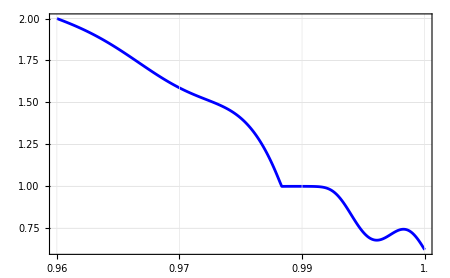

```mathematica
ThesisStandardPlotTime[Mach[rbarNumIn[x tFinish],urNumIn[x tFinish],uphiNumIn[x tFinish]],(*The function to plot*){x,NearSubsonicTime[[1,1]]/tFinish,1},(*The range of t*)"Fig_Mach_Number_Evolution",(*Filename*)"\\mathcal{M}(t)",(*y-label*)"t",(*x-label*){},(*No legends/labels*)None,(*Set to tSurface if you want the vertical line*)250,(*Higher PlotPoints for the Mach step*)30                                            (*WorkingPrecision for stability*)]
```

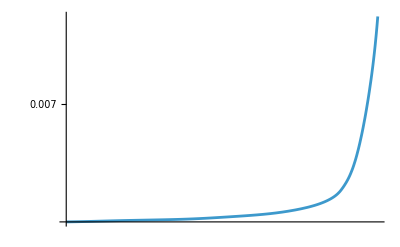

```mathematica
LogLogPlot[massNumIn[t],{t,1.4 10^10,1.6 10^10}, PlotRange->All]
```

Saved Matched Log-Log: /home/em/Documents/thesis/sun_density/Fig_Mass_Growth_Final_LogLog.pdf

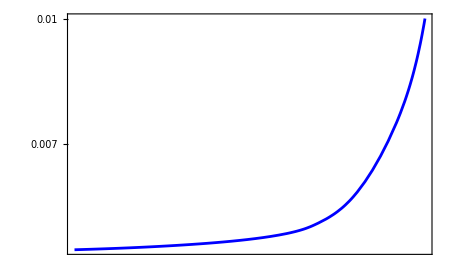

```mathematica
Show[ThesisStandardLogLogPlot[massNumIn[t],{t,1.52 10^10,1.6103 10^10},"Fig_Mass_Growth_Final_LogLog"], PlotRange->All]
```

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFunc[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/sun_density/Fig_Gravitational_Wave_Plus.pdf

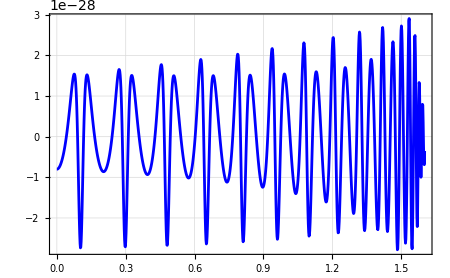

```mathematica
ThesisStandardPlot[{hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]]},{t,0,tFinish},"Fig_Gravitational_Wave_Plus","h_{+}(t)","t",{},(*No labels for a single curve*)None,(*No special xTick*)1000,(*pPoints:High initial sampling for fast oscillations*)60       (*wPrec:High precision to resolve 10^-23 amplitudes*)]
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFunc[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

```mathematica
(*10^18 for distance from earth to the galactic halo*)
```

Saved Standard (High-Precision): /home/em/Documents/thesis/sun_density/Fig_Gravitational_Wave_Polarisations.pdf

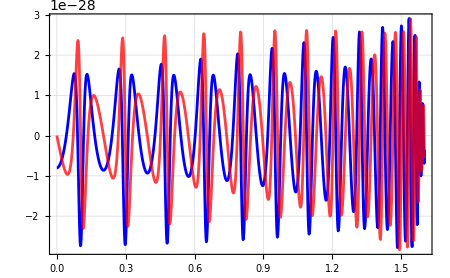

```mathematica
ThesisStandardPlotPOL[{hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]], hxFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]]},{t,0,tFinish},"Fig_Gravitational_Wave_Polarisations","h_+(t), \\text{ } h_{\\times}(t)","t",{},(*No labels for a single curve*)None,(*No special xTick*)1000,(*pPoints:High initial sampling for fast oscillations*)60       (*wPrec:High precision to resolve 10^-23 amplitudes*)]
```

```mathematica
hplus[t_]:= hplusFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]] 
hcross[t_]:= hxFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]]
```

```mathematica
hNorm[t_] := Abs[hplusFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]] - I*hxFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]]]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/sun_density/Fig_Strain_Dashed_Final.pdf

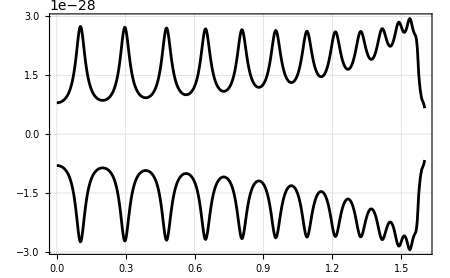

```mathematica
ThesisStandardPlot[{hNorm[t],-hNorm[t]},{t,0,tFinish},"Fig_Strain_Dashed_Final","h(t)","t",{},None,500,(*High sampling for waves*)30,(*High precision*){Directive[Black],(*hNorm top*)Directive[Black]    (*hNorm bottom*)}]
```

```mathematica
(*Obtaining 5 troughs in the middle*)
```

```mathematica
fgeom = 5/((1.09 10^10)-(4.81 10^9))
```

8.21018×10^-10

```mathematica
fHz = fgeom/(5 10^-6)
```

0.000164204

```mathematica
fHz/10^-4
```

1.64204